-Graphics- |   Métodos Computacionales en Álgebra para Informáticos
Matemática Discreta y Lógica
Dpto. de Matemáticas. Área de  Álgebra  (M. A. García, C. Ordóñez, J. F. Ruiz)

# Capítulo 3 Polinomio. Cálculos básicos y Divisibilidad

## 1. Listas

#### Ejemplo 3.1.

Introducimos la lista l={2, x, π/2,3+i}.

```mathematica
l={2,x,Pi/2,3+I};
```

Observemos que tenemos elementos de distinta naturaleza y que podremos multiplicar todos sus elementos por 2

```mathematica
h=2*l
```

{4,2 x,π,6+2 ⅈ}

o calcular una aproximación decimal del seno de cada uno de los elementos de la lista

```mathematica
Sin[h]//N
```

{-0.756802,Sin[2. x],0.,-1.05122+3.4824 ⅈ}

Las listas pueden estar formadas por elementos de distintos tipos, por ejemplo :

```mathematica
l2={{},{1,2},x,4,{4},{{4}},rojo};
```

Esta lista está formada por 7 elementos, entre los que encontramos un número, 4, dos variables, 'x' y 'rojo', una lista vacía, {}, otra con un elemento, {4}, y otra más que contiene a su vez otra lista, {{4}}.

#### Ejemplo 3.2.

Consideramos un par de listas y probamos con ellas las distintas funciones que aparecen en el cuadro anterior 3.1.

```mathematica
lista1={0,2,-7,y,4,3x^2+1,E,5+2I};
lista2={a,l,g,e,b,r,a};
```

```mathematica
Length[lista1]
Length[lista2]
```

8

7

Podemos juntarlas y obtener una nueva lista :

```mathematica
lista3=Join[lista1,lista2]
Length[lista3]
```

{0,2,-7,y,4,1+3 x^2,ⅇ,5+2 ⅈ,a,l,g,e,b,r,a}

15

Así vemos que la nueva lista tiene 7 + 8 = 15 elementos.Para obtener el elemento que ocupa el cuarto lugar de "lista1" :

```mathematica
lista1[[4]]
```

y

Si queremos saber el primer y último elemento, respectivamente :

```mathematica
First[lista1]
Last[lista1]
```

0

5+2 ⅈ

Añadiremos, al final de la lista, el elemento α

```mathematica
Append[lista1,α]
```

{0,2,-7,y,4,1+3 x^2,ⅇ,5+2 ⅈ,α}

Observemos que el valor de "lista1" no varía

```mathematica
lista1
```

{0,2,-7,y,4,1+3 x^2,ⅇ,5+2 ⅈ}

Sin embargo si añadimos, al final de la lista, el elemento α, con la función AppendTo

```mathematica
AppendTo[lista1,α]
```

{0,2,-7,y,4,1+3 x^2,ⅇ,5+2 ⅈ,α}

el resultado parece el mismo, pero lo que ha cambiado es el contenido de "lista1".En efecto,

```mathematica
lista1
```

{0,2,-7,y,4,1+3 x^2,ⅇ,5+2 ⅈ,α}

Análogamente, podremos añadir un elemento al principio de la lista; por ejemplo, 2 π :

```mathematica
Prepend[lista1,2Pi]
```

{2 π,0,2,-7,y,4,1+3 x^2,ⅇ,5+2 ⅈ,α}

```mathematica
lista1
```

{0,2,-7,y,4,1+3 x^2,ⅇ,5+2 ⅈ,α}

```mathematica
PrependTo[lista1,2Pi]
```

{2 π,0,2,-7,y,4,1+3 x^2,ⅇ,5+2 ⅈ,α}

```mathematica
lista1
```

{2 π,0,2,-7,y,4,1+3 x^2,ⅇ,5+2 ⅈ,α}

Si ahora quisiéramos obtener una nueva lista, eliminando de la anterior el número e :

```mathematica
lista4=Delete[lista1,8]
```

{2 π,0,2,-7,y,4,1+3 x^2,5+2 ⅈ,α}

También podríamos estar interesados en una lista, en la que añadiéramos a la anterior el elemento y + 7, en la segunda posición.Para ello, escribiremos :

```mathematica
lista5=Insert[lista4,y+7,2]
```

{2 π,7+y,0,2,-7,y,4,1+3 x^2,5+2 ⅈ,α}

Ahora, a "lista3" le quitamos los primeros 5 elementos :

```mathematica
lista6=Drop[lista3,5]
```

{1+3 x^2,ⅇ,5+2 ⅈ,a,l,g,e,b,r,a}

Ordenamos con Sort[] los elementos y probamos Ordering[] (la posición que ocupa cada elemento) :

```mathematica
lista7=Sort[lista6]
lista8=Ordering[lista6]
```

{5+2 ⅈ,a,a,b,e,ⅇ,g,l,r,1+3 x^2}

{3,4,10,8,7,2,6,5,9,1}

Ahora recuperamos desde "lista6" los elementos de "lista2" y buscamos las posiciones en las que está la letra 'a' :

```mathematica
Take[lista6,{4,10}]
```

{a,l,g,e,b,r,a}

```mathematica
Position[%,a]
```

{{1},{7}}

Por último, probamos en "lista8" las funciones TakeWhile[] y Select[] con el test "PrimeQ" (esto es, si es un número primo) :

```mathematica
TakeWhile[lista8,PrimeQ]
```

{3}

```mathematica
Select[lista8,PrimeQ]
```

{3,7,2,5}

## 2. La función Table

#### Ejemplo 3.3.

Calcular, utilizando la función Table[], una lista formada por los cinco primeros múltiplos positivos de 3.

```mathematica
v=Table[3i,{i,1,5,1}]
```

{3,6,9,12,15}

O bien,

```mathematica
v=Table[i,{i,1,15,3}
```

#### Ejemplo 3.4.

Crear una tabla 2×4, utilizando la función Table[], cuya primera fila sea los números positivos pares, menores de 10 y la segunda los cuadrados de los números de la primera fila.

```mathematica
a=Table[(2*j)^i,{i,2},{j,4}]
```

{{2,4,6,8},{4,16,36,64}}

#### Ejemplo 3.5.

Para que las listas de los ejemplos 3.3. y 3.4. adopten un formato de tabla podríamos escribir

```mathematica
TableForm[v]
TableForm[a]
```

3
6
9
12
15

2 | 4 | 6 | 8
4 | 16 | 36 | 64

#### Ejemplo 3.6.

Otra forma de definir la lista del ejemplo 3.3., v={3, 6, 9, 12, 15}, utilizando la función Table[], podría ser detallando todos sus elementos.

```mathematica
v=Table[0,{i,5}];
v[[1]]=3;
v[[2]]=6;
v[[3]]=9;
v[[4]]=12;
v[[5]]=15;
v
```

{3,6,9,12,15}

También podemos definir la tabla del ejemplo 3.4.,  a={{2, 4, 6, 8}, {4, 16, 36, 64}}, utilizando la función Table[] y especificando todos sus elementos:

```mathematica
a=Table[0,{i,2},{j,4}];
a[[1,1]]=2;
a[[1,2]]=4;
a[[1,3]]=6;
a[[1,4]]=8;
a[[2,1]]=4;
a[[2,2]]=16;
a[[2,3]]=36;
a[[2,4]]=64;
a
```

{{2,4,6,8},{4,16,36,64}}

## 3. Vectores y matrices

#### Ejemplo 3.7.

Para trabajar con el vector (-1, 2, 0)∈ ℝ^3introduciremos

```mathematica
u={-1,2,0};
```

#### Ejemplo 3.8.

La matriz b=(1 | 2 | 3
2 | -3 | 0) podemos interpretarla como una lista de sus filas y así escribiremos

```mathematica
b={{1,2,3},{2,-3,0}};
```

#### Ejemplo 3.9.

Para que aparezcan los paréntesis del vector u o de la matriz b de los dos ejemplos anteriores podremos escribir

```mathematica
MatrixForm[u]
MatrixForm[b]
```

(-1
2
0)

(1 | 2 | 3
2 | -3 | 0)

Observemos en la siguiente salida cómo MatrixForm[] devuelve una representación gráfica de una lista y no podemos utilizarla para operar con ella

```mathematica
M=MatrixForm[u];
M[[3]]
```

Part::partw: Part 3 of ( GridBox[{{-1}, { does not exist. More…

(-1
2
0)⟦3⟧

```mathematica
b={{1,2,3},{2,-3,0}}//MatrixForm
```

(1 | 2 | 3
2 | -3 | 0)

```mathematica
b[[2]]
```

Part::partw: Part 2 of (1 | 2 | 3
2 | -3 | 0) does not exist.

(1 | 2 | 3
2 | -3 | 0)⟦2⟧

#### Ejemplo 3.10.

Obtenemos el número de coordenadas de u y el orden de la matriz b a través de

```mathematica
Dimensions[u]
Dimensions[b]
```

{3}

{2,3}

#### Ejemplo 3.11.

Para describir con Mathematica el vector (A, B, C, D) podremos hacer

```mathematica
vector={A,B,C,D}
```

{A,B,C,D}

o bien

```mathematica
vector=Table[0,{i,4}];
vector[[1]]=A;
vector[[2]]=B;
vector[[3]]=C;
vector[[4]]=D;
vector
```

{A,B,C,D}

#### Ejemplo 3.12.

Para definir la matriz 3×3 que contiene cero en todas sus coordenadas escribiremos

```mathematica
matriz=Table[0,{i,3},{j,3}]
```

General::spell1: Possible spelling error: new symbol name "matriz" is similar to existing symbol "Matriz". More…

{{0,0,0},{0,0,0},{0,0,0}}

```mathematica
MatrixForm[matriz]
```

(0 | 0 | 0
0 | 0 | 0
0 | 0 | 0)

y en forma de tabla

```mathematica
TableForm[matriz]
```

0 | 0 | 0
0 | 0 | 0
0 | 0 | 0

Análogamente, a la lista siguiente podemos darle aspecto de matriz o de tabla

```mathematica
matriz={{1,2,3}, {4,5,6},{7,8,9}};
MatrixForm[matriz]
TableForm[matriz]
```

(1 | 2 | 3
4 | 5 | 6
7 | 8 | 9)

1 | 2 | 3
4 | 5 | 6
7 | 8 | 9

## 4. Representación y formato de una lista

#### Ejemplo 3.13.

En este ejemplo vemos como representar distintos tipos de tablas y matrices con MatrixForm[] y TableForm[], para ello vamos a generar y representar una tabla con todos los productos de todas las matrices booleanas (compuestas únicamente por ceros y unos) de dos filas y dos columnas:

```mathematica
matricesbooleanas=Table[{{IntegerDigits[i,2,4][[1]],IntegerDigits[i,2,4][[2]]},{IntegerDigits[i,2,4][[3]],IntegerDigits[i,2,4][[4]]}},{i,0,15}];
TableForm[Table[MatrixForm[matricesbooleanas[[i]].matricesbooleanas[[j]]],{i,16},{j,16}],TableHeadings->{Table[MatrixForm[matricesbooleanas[[i]]],{i,16}],Table[MatrixForm[matricesbooleanas[[i]]],{i,16}]}]
```

| (0 | 0
0 | 0) | (0 | 0
0 | 1) | (0 | 0
1 | 0) | (0 | 0
1 | 1) | (0 | 1
0 | 0) | (0 | 1
0 | 1) | (0 | 1
1 | 0) | (0 | 1
1 | 1) | (1 | 0
0 | 0) | (1 | 0
0 | 1) | (1 | 0
1 | 0) | (1 | 0
1 | 1) | (1 | 1
0 | 0) | (1 | 1
0 | 1) | (1 | 1
1 | 0) | (1 | 1
1 | 1)
(0 | 0
0 | 0) | (0 | 0
0 | 0) | (0 | 0
0 | 0) | (0 | 0
0 | 0) | (0 | 0
0 | 0) | (0 | 0
0 | 0) | (0 | 0
0 | 0) | (0 | 0
0 | 0) | (0 | 0
0 | 0) | (0 | 0
0 | 0) | (0 | 0
0 | 0) | (0 | 0
0 | 0) | (0 | 0
0 | 0) | (0 | 0
0 | 0) | (0 | 0
0 | 0) | (0 | 0
0 | 0) | (0 | 0
0 | 0)
(0 | 0
0 | 1) | (0 | 0
0 | 0) | (0 | 0
0 | 1) | (0 | 0
1 | 0) | (0 | 0
1 | 1) | (0 | 0
0 | 0) | (0 | 0
0 | 1) | (0 | 0
1 | 0) | (0 | 0
1 | 1) | (0 | 0
0 | 0) | (0 | 0
0 | 1) | (0 | 0
1 | 0) | (0 | 0
1 | 1) | (0 | 0
0 | 0) | (0 | 0
0 | 1) | (0 | 0
1 | 0) | (0 | 0
1 | 1)
(0 | 0
1 | 0) | (0 | 0
0 | 0) | (0 | 0
0 | 0) | (0 | 0
0 | 0) | (0 | 0
0 | 0) | (0 | 0
0 | 1) | (0 | 0
0 | 1) | (0 | 0
0 | 1) | (0 | 0
0 | 1) | (0 | 0
1 | 0) | (0 | 0
1 | 0) | (0 | 0
1 | 0) | (0 | 0
1 | 0) | (0 | 0
1 | 1) | (0 | 0
1 | 1) | (0 | 0
1 | 1) | (0 | 0
1 | 1)
(0 | 0
1 | 1) | (0 | 0
0 | 0) | (0 | 0
0 | 1) | (0 | 0
1 | 0) | (0 | 0
1 | 1) | (0 | 0
0 | 1) | (0 | 0
0 | 2) | (0 | 0
1 | 1) | (0 | 0
1 | 2) | (0 | 0
1 | 0) | (0 | 0
1 | 1) | (0 | 0
2 | 0) | (0 | 0
2 | 1) | (0 | 0
1 | 1) | (0 | 0
1 | 2) | (0 | 0
2 | 1) | (0 | 0
2 | 2)
(0 | 1
0 | 0) | (0 | 0
0 | 0) | (0 | 1
0 | 0) | (1 | 0
0 | 0) | (1 | 1
0 | 0) | (0 | 0
0 | 0) | (0 | 1
0 | 0) | (1 | 0
0 | 0) | (1 | 1
0 | 0) | (0 | 0
0 | 0) | (0 | 1
0 | 0) | (1 | 0
0 | 0) | (1 | 1
0 | 0) | (0 | 0
0 | 0) | (0 | 1
0 | 0) | (1 | 0
0 | 0) | (1 | 1
0 | 0)
(0 | 1
0 | 1) | (0 | 0
0 | 0) | (0 | 1
0 | 1) | (1 | 0
1 | 0) | (1 | 1
1 | 1) | (0 | 0
0 | 0) | (0 | 1
0 | 1) | (1 | 0
1 | 0) | (1 | 1
1 | 1) | (0 | 0
0 | 0) | (0 | 1
0 | 1) | (1 | 0
1 | 0) | (1 | 1
1 | 1) | (0 | 0
0 | 0) | (0 | 1
0 | 1) | (1 | 0
1 | 0) | (1 | 1
1 | 1)
(0 | 1
1 | 0) | (0 | 0
0 | 0) | (0 | 1
0 | 0) | (1 | 0
0 | 0) | (1 | 1
0 | 0) | (0 | 0
0 | 1) | (0 | 1
0 | 1) | (1 | 0
0 | 1) | (1 | 1
0 | 1) | (0 | 0
1 | 0) | (0 | 1
1 | 0) | (1 | 0
1 | 0) | (1 | 1
1 | 0) | (0 | 0
1 | 1) | (0 | 1
1 | 1) | (1 | 0
1 | 1) | (1 | 1
1 | 1)
(0 | 1
1 | 1) | (0 | 0
0 | 0) | (0 | 1
0 | 1) | (1 | 0
1 | 0) | (1 | 1
1 | 1) | (0 | 0
0 | 1) | (0 | 1
0 | 2) | (1 | 0
1 | 1) | (1 | 1
1 | 2) | (0 | 0
1 | 0) | (0 | 1
1 | 1) | (1 | 0
2 | 0) | (1 | 1
2 | 1) | (0 | 0
1 | 1) | (0 | 1
1 | 2) | (1 | 0
2 | 1) | (1 | 1
2 | 2)
(1 | 0
0 | 0) | (0 | 0
0 | 0) | (0 | 0
0 | 0) | (0 | 0
0 | 0) | (0 | 0
0 | 0) | (0 | 1
0 | 0) | (0 | 1
0 | 0) | (0 | 1
0 | 0) | (0 | 1
0 | 0) | (1 | 0
0 | 0) | (1 | 0
0 | 0) | (1 | 0
0 | 0) | (1 | 0
0 | 0) | (1 | 1
0 | 0) | (1 | 1
0 | 0) | (1 | 1
0 | 0) | (1 | 1
0 | 0)
(1 | 0
0 | 1) | (0 | 0
0 | 0) | (0 | 0
0 | 1) | (0 | 0
1 | 0) | (0 | 0
1 | 1) | (0 | 1
0 | 0) | (0 | 1
0 | 1) | (0 | 1
1 | 0) | (0 | 1
1 | 1) | (1 | 0
0 | 0) | (1 | 0
0 | 1) | (1 | 0
1 | 0) | (1 | 0
1 | 1) | (1 | 1
0 | 0) | (1 | 1
0 | 1) | (1 | 1
1 | 0) | (1 | 1
1 | 1)
(1 | 0
1 | 0) | (0 | 0
0 | 0) | (0 | 0
0 | 0) | (0 | 0
0 | 0) | (0 | 0
0 | 0) | (0 | 1
0 | 1) | (0 | 1
0 | 1) | (0 | 1
0 | 1) | (0 | 1
0 | 1) | (1 | 0
1 | 0) | (1 | 0
1 | 0) | (1 | 0
1 | 0) | (1 | 0
1 | 0) | (1 | 1
1 | 1) | (1 | 1
1 | 1) | (1 | 1
1 | 1) | (1 | 1
1 | 1)
(1 | 0
1 | 1) | (0 | 0
0 | 0) | (0 | 0
0 | 1) | (0 | 0
1 | 0) | (0 | 0
1 | 1) | (0 | 1
0 | 1) | (0 | 1
0 | 2) | (0 | 1
1 | 1) | (0 | 1
1 | 2) | (1 | 0
1 | 0) | (1 | 0
1 | 1) | (1 | 0
2 | 0) | (1 | 0
2 | 1) | (1 | 1
1 | 1) | (1 | 1
1 | 2) | (1 | 1
2 | 1) | (1 | 1
2 | 2)
(1 | 1
0 | 0) | (0 | 0
0 | 0) | (0 | 1
0 | 0) | (1 | 0
0 | 0) | (1 | 1
0 | 0) | (0 | 1
0 | 0) | (0 | 2
0 | 0) | (1 | 1
0 | 0) | (1 | 2
0 | 0) | (1 | 0
0 | 0) | (1 | 1
0 | 0) | (2 | 0
0 | 0) | (2 | 1
0 | 0) | (1 | 1
0 | 0) | (1 | 2
0 | 0) | (2 | 1
0 | 0) | (2 | 2
0 | 0)
(1 | 1
0 | 1) | (0 | 0
0 | 0) | (0 | 1
0 | 1) | (1 | 0
1 | 0) | (1 | 1
1 | 1) | (0 | 1
0 | 0) | (0 | 2
0 | 1) | (1 | 1
1 | 0) | (1 | 2
1 | 1) | (1 | 0
0 | 0) | (1 | 1
0 | 1) | (2 | 0
1 | 0) | (2 | 1
1 | 1) | (1 | 1
0 | 0) | (1 | 2
0 | 1) | (2 | 1
1 | 0) | (2 | 2
1 | 1)
(1 | 1
1 | 0) | (0 | 0
0 | 0) | (0 | 1
0 | 0) | (1 | 0
0 | 0) | (1 | 1
0 | 0) | (0 | 1
0 | 1) | (0 | 2
0 | 1) | (1 | 1
0 | 1) | (1 | 2
0 | 1) | (1 | 0
1 | 0) | (1 | 1
1 | 0) | (2 | 0
1 | 0) | (2 | 1
1 | 0) | (1 | 1
1 | 1) | (1 | 2
1 | 1) | (2 | 1
1 | 1) | (2 | 2
1 | 1)
(1 | 1
1 | 1) | (0 | 0
0 | 0) | (0 | 1
0 | 1) | (1 | 0
1 | 0) | (1 | 1
1 | 1) | (0 | 1
0 | 1) | (0 | 2
0 | 2) | (1 | 1
1 | 1) | (1 | 2
1 | 2) | (1 | 0
1 | 0) | (1 | 1
1 | 1) | (2 | 0
2 | 0) | (2 | 1
2 | 1) | (1 | 1
1 | 1) | (1 | 2
1 | 2) | (2 | 1
2 | 1) | (2 | 2
2 | 2)

#### Ejemplo 3.14.

En este ejemplo practicamos el uso de Column[], Row[] y Multicolumn[], para ello generamos las tablas de multiplicar del 1 al 10:

```mathematica
Column[{Text[Style["Tablas de multiplicar",Large,Bold,Brown]],Multicolumn[Table[Column[Table[Row[{i," × ",j," = ",i*j}],{j,1,10}]],{i,1,10}],5,Background->{{{LightOrange,LightGreen}},{{LightYellow,White}}},Frame->All,FrameStyle->White]},Alignment->{Center},Frame->All,Background->LightYellow]
```

Tablas de multiplicar
1 × 1 = 1
1 × 2 = 2
1 × 3 = 3
1 × 4 = 4
1 × 5 = 5
1 × 6 = 6
1 × 7 = 7
1 × 8 = 8
1 × 9 = 9
1 × 10 = 10 | 3 × 1 = 3
3 × 2 = 6
3 × 3 = 9
3 × 4 = 12
3 × 5 = 15
3 × 6 = 18
3 × 7 = 21
3 × 8 = 24
3 × 9 = 27
3 × 10 = 30 | 5 × 1 = 5
5 × 2 = 10
5 × 3 = 15
5 × 4 = 20
5 × 5 = 25
5 × 6 = 30
5 × 7 = 35
5 × 8 = 40
5 × 9 = 45
5 × 10 = 50 | 7 × 1 = 7
7 × 2 = 14
7 × 3 = 21
7 × 4 = 28
7 × 5 = 35
7 × 6 = 42
7 × 7 = 49
7 × 8 = 56
7 × 9 = 63
7 × 10 = 70 | 9 × 1 = 9
9 × 2 = 18
9 × 3 = 27
9 × 4 = 36
9 × 5 = 45
9 × 6 = 54
9 × 7 = 63
9 × 8 = 72
9 × 9 = 81
9 × 10 = 90
2 × 1 = 2
2 × 2 = 4
2 × 3 = 6
2 × 4 = 8
2 × 5 = 10
2 × 6 = 12
2 × 7 = 14
2 × 8 = 16
2 × 9 = 18
2 × 10 = 20 | 4 × 1 = 4
4 × 2 = 8
4 × 3 = 12
4 × 4 = 16
4 × 5 = 20
4 × 6 = 24
4 × 7 = 28
4 × 8 = 32
4 × 9 = 36
4 × 10 = 40 | 6 × 1 = 6
6 × 2 = 12
6 × 3 = 18
6 × 4 = 24
6 × 5 = 30
6 × 6 = 36
6 × 7 = 42
6 × 8 = 48
6 × 9 = 54
6 × 10 = 60 | 8 × 1 = 8
8 × 2 = 16
8 × 3 = 24
8 × 4 = 32
8 × 5 = 40
8 × 6 = 48
8 × 7 = 56
8 × 8 = 64
8 × 9 = 72
8 × 10 = 80 | 10 × 1 = 10
10 × 2 = 20
10 × 3 = 30
10 × 4 = 40
10 × 5 = 50
10 × 6 = 60
10 × 7 = 70
10 × 8 = 80
10 × 9 = 90
10 × 10 = 100

#### Ejemplo 3.15.

Mathematica trae tablas predefinidas que también podemos usar. En este ejemplo vamos a representar la tabla periódica de elementos, necesitamos una tabla de 18 columnas y 10 filas, dejaremos sin rellenar las celdas de la tabla donde no haya ningún elemento de forma que la tabla quede en la representación habitual:

```mathematica
tablaperiodica={{"H", , , , , , , , , , , , , , , , ,"He"},{"Li","Be", , ,
, , , , , , , ,"B","C","N","O","F","Ne"},{"Na","Mg", , , , , , ,
, , , ,"Al","Si","P","S","Cl","Ar"},{"K","Ca","Sc","Ti","V","Cr","Mn","Fe","Co","Ni","Cu","Zn","Ga","Ge","As","Se","Br","Kr"},{"Rb","Sr","Y","Zr","Nb","Mo","Tc","Ru","Rh","Pd","Ag","Cd","In","Sn","Sb","Te","I","Xe"},{"Cs","Ba", ,"Hf","Ta","W","Re","Os","Ir","Pt","Au","Hg","Tl","Pb","Bi","Po","At","Rn"},{"Fr","Ra", ,"Rf","Db","Sg","Bh","Hs","Mt","Ds","Rg","Uub","Uut","Uuq","Uup","Uuh","Uus","Uuo"},{},{, ,"La","Ce","Pr","Nd","Pm","Sm","Eu","Gd","Tb","Dy","Ho","Er","Tm","Yb","Lu",},{, ,"Ac","Th","Pa","U","Np","Pu","Am","Cm","Bk","Cf","Es","Fm","Md","No","Lr",}};
Grid[tablaperiodica]
```

H |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | He
Li | Be |  |  |  |  |  |  |  |  |  |  | B | C | N | O | F | Ne
Na | Mg |  |  |  |  |  |  |  |  |  |  | Al | Si | P | S | Cl | Ar
K | Ca | Sc | Ti | V | Cr | Mn | Fe | Co | Ni | Cu | Zn | Ga | Ge | As | Se | Br | Kr
Rb | Sr | Y | Zr | Nb | Mo | Tc | Ru | Rh | Pd | Ag | Cd | In | Sn | Sb | Te | I | Xe
Cs | Ba |  | Hf | Ta | W | Re | Os | Ir | Pt | Au | Hg | Tl | Pb | Bi | Po | At | Rn
Fr | Ra |  | Rf | Db | Sg | Bh | Hs | Mt | Ds | Rg | Uub | Uut | Uuq | Uup | Uuh | Uus | Uuo
 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  | La | Ce | Pr | Nd | Pm | Sm | Eu | Gd | Tb | Dy | Ho | Er | Tm | Yb | Lu | 
 |  | Ac | Th | Pa | U | Np | Pu | Am | Cm | Bk | Cf | Es | Fm | Md | No | Lr |

Podemos obtenerla directamente porque ya está implementada en Mathematica así:

```mathematica
ColorData["Atoms","Panel"]
```

#### Ejemplo 3.16.

Las fotografías, dibujos, o imágenes pueden representarse como una tabla o matriz con las mismas dimensiones que la imagen y donde cada celda o coordenada representa un pixel, habitualmente el color o cualquier otra propiedad de la imagen. En el siguiente ejemplo vamos a trabajar con una imagen como si fuese una tabla. Consideramos la siguiente imagen:

```mathematica
imagen=Import["K:\LIBRO ALGEBRA I\2.aa EDICIÓN\Mathematica\ujaencolorpeq.jpg"]
```

-Graphics-

```mathematica
imagentabla=ImageData[ColorNegate[imagen]];
SetPrecision[Take[imagentabla,{1,8},{1,8}],6]//MatrixForm
```

((0
0.00784314
0.00784314) | (0
0
0.0156863) | (0.00392157
0
0.0156863) | (0.0156863
0
0.0156863) | (0.0156863
0
0) | (0.0117647
0
0) | (0
0
0.0156863) | (0
0
0.0156863)
(0
0.00784314
0.00784314) | (0
0.00392157
0.00784314) | (0.0117647
0
0.0156863) | (0.0156863
0
0.00784314) | (0.0117647
0
0.00784314) | (0
0
0.00784314) | (0
0
0.00784314) | (0
0
0.00784314)
(0
0.00784314
0.0156863) | (0
0.00392157
0.00784314) | (0.0117647
0
0) | (0.0117647
0
0.00784314) | (0
0
0.0196078) | (0
0
0.0196078) | (0
0.00392157
0) | (0
0.00392157
0)
(0
0.00392157
0.00784314) | (0
0.00392157
0) | (0.00392157
0
0) | (0.00392157
0
0) | (0
0.00392157
0.0196078) | (0
0.00392157
0.0156863) | (0
0.00392157
0) | (0
0.00392157
0)
(0.00392157
0
0) | (0.00392157
0
0) | (0
0.00392157
0) | (0
0.00784314
0) | (0
0.0117647
0) | (0
0.0117647
0) | (0
0.00392157
0) | (0
0
0)
(0.0117647
0
0) | (0.00392157
0
0) | (0
0.00392157
0) | (0
0.00784314
0) | (0
0.00784314
0) | (0
0.00392157
0) | (0
0.00392157
0) | (0.00392157
0
0)
(0
0
0) | (0
0.00392157
0) | (0
0.00784314
0) | (0
0.00392157
0) | (0
0
0) | (0.0117647
0
0) | (0.0156863
0
0) | (0.0117647
0
0)
(0
0.00392157
0) | (0
0.00392157
0) | (0
0.00392157
0) | (0
0
0) | (0.00392157
0
0.00784314) | (0.0156863
0
0.00784314) | (0.0235294
0
0) | (0.0156863
0
0.00784314))

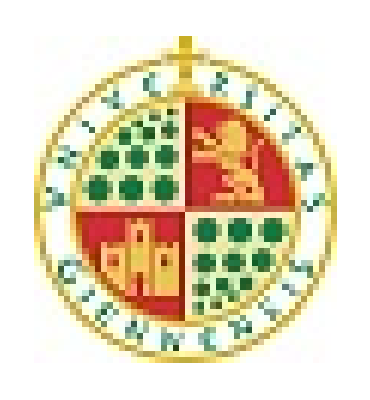

```mathematica
ArrayPlot[imagentabla]
```

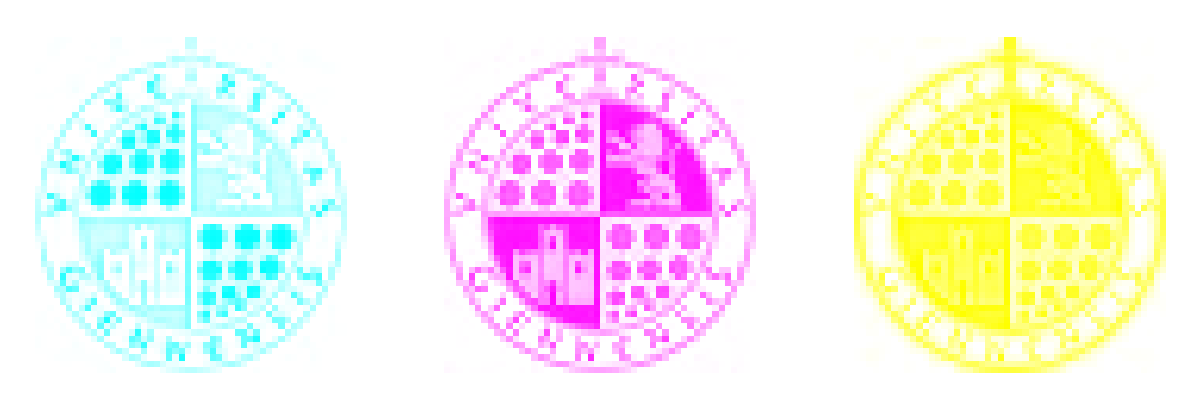

```mathematica
imagentablacian=Table[{imagentabla[[i,j]][[1]],0.,0.},{i,Length[imagentabla]},{j,Length[imagentabla[[1]]]}];
imagentablamagenta=Table[{0.,imagentabla[[i,j]][[2]],0.},{i,Length[imagentabla]},{j,Length[imagentabla[[1]]]}];
imagentablaamarillo=Table[{0.,0.,imagentabla[[i,j]][[3]]},{i,Length[imagentabla]},{j,Length[imagentabla[[1]]]}];
GraphicsRow[{ArrayPlot[imagentablacian],ArrayPlot[imagentablamagenta],ArrayPlot[imagentablaamarillo]}]
```

## 5. Ejercicios

#### Ejercicio 3.9.

Calendario perpetuo

```mathematica
años=Table[If[1901>1896+i+(28*(j-2))||1896+i+(28*(j-2))>2099,"-",1896+i+(28*(j-2))],{i,28},{j,9}];
Do[años[[i,1]]=i,{i,28}];
TableForm[años]
```

1 | - | 1925 | 1953 | 1981 | 2009 | 2037 | 2065 | 2093
2 | - | 1926 | 1954 | 1982 | 2010 | 2038 | 2066 | 2094
3 | - | 1927 | 1955 | 1983 | 2011 | 2039 | 2067 | 2095
4 | - | 1928 | 1956 | 1984 | 2012 | 2040 | 2068 | 2096
5 | 1901 | 1929 | 1957 | 1985 | 2013 | 2041 | 2069 | 2097
6 | 1902 | 1930 | 1958 | 1986 | 2014 | 2042 | 2070 | 2098
7 | 1903 | 1931 | 1959 | 1987 | 2015 | 2043 | 2071 | 2099
8 | 1904 | 1932 | 1960 | 1988 | 2016 | 2044 | 2072 | -
9 | 1905 | 1933 | 1961 | 1989 | 2017 | 2045 | 2073 | -
10 | 1906 | 1934 | 1962 | 1990 | 2018 | 2046 | 2074 | -
11 | 1907 | 1935 | 1963 | 1991 | 2019 | 2047 | 2075 | -
12 | 1908 | 1936 | 1964 | 1992 | 2020 | 2048 | 2076 | -
13 | 1909 | 1937 | 1965 | 1993 | 2021 | 2049 | 2077 | -
14 | 1910 | 1938 | 1966 | 1994 | 2022 | 2050 | 2078 | -
15 | 1911 | 1939 | 1967 | 1995 | 2023 | 2051 | 2079 | -
16 | 1912 | 1940 | 1968 | 1996 | 2024 | 2052 | 2080 | -
17 | 1913 | 1941 | 1969 | 1997 | 2025 | 2053 | 2081 | -
18 | 1914 | 1942 | 1970 | 1998 | 2026 | 2054 | 2082 | -
19 | 1915 | 1943 | 1971 | 1999 | 2027 | 2055 | 2083 | -
20 | 1916 | 1944 | 1972 | 2000 | 2028 | 2056 | 2084 | -
21 | 1917 | 1945 | 1973 | 2001 | 2029 | 2057 | 2085 | -
22 | 1918 | 1946 | 1974 | 2002 | 2030 | 2058 | 2086 | -
23 | 1919 | 1947 | 1975 | 2003 | 2031 | 2059 | 2087 | -
24 | 1920 | 1948 | 1976 | 2004 | 2032 | 2060 | 2088 | -
25 | 1921 | 1949 | 1977 | 2005 | 2033 | 2061 | 2089 | -
26 | 1922 | 1950 | 1978 | 2006 | 2034 | 2062 | 2090 | -
27 | 1923 | 1951 | 1979 | 2007 | 2035 | 2063 | 2091 | -
28 | 1924 | 1952 | 1980 | 2008 | 2036 | 2064 | 2092 | -

```mathematica
meses={{4,0,0,3,5,1,3,6,2,4,0,2},{5,1,1,4,6,2,4,0,3,5,1,3},{6,2,2,5,0,3,5,1,4,6,2,4},{0,3,4,0,2,5,0,3,6,1,4,6},{2,5,5,1,3,6,1,4,0,2,5,0},{3,6,6,2,4,0,2,5,1,3,6,1},{4,0,0,3,5,1,3,6,2,4,0,2},{5,1,2,5,0,3,5,1,4,6,2,4},{0,3,3,6,1,4,6,2,5,0,3,5},{1,4,4,0,2,5,0,3,6,1,4,6},{2,5,5,1,3,6,1,4,0,2,5,0},{3,6,0,3,5,1,3,6,2,4,0,2},{5,1,1,4,6,2,4,0,3,5,1,3},{6,2,2,5,0,3,5,1,4,6,2,4},{0,3,3,6,1,4,6,2,5,0,3,5},{1,4,5,1,3,6,1,4,0,2,5,0},{3,6,6,2,4,0,2,5,1,3,6,1},{4,0,0,3,5,1,3,6,2,4,0,2},{5,1,1,4,6,2,4,0,3,5,1,3},{6,2,3,6,1,4,6,2,5,0,3,5},{1,4,4,0,2,5,0,3,6,1,4,6},{2,5,5,1,3,6,1,4,0,2,5,0},{3,6,6,2,4,0,2,5,1,3,6,1},{4,0,1,4,6,2,4,0,3,5,1,3},{6,2,2,5,0,3,5,1,4,6,2,4},{0,3,3,6,1,4,6,2,5,0,3,5},{1,4,4,0,2,5,0,3,6,1,4,6}};
```

```mathematica
dia=Table[If[0>(i+7*(j-2))||(i+7*(j-2))>37,"-",i+7*(j-2)],{i,7},{j,7}];
dia[[1,1]]=Domingo;dia[[2,1]]=Lunes;dia[[3,1]]=Martes;
dia[[4,1]]=Miercoles;dia[[5,1]]=Jueves;dia[[6,1]]=Viernes;
dia[[7,1]]=Sabado;
TableForm[dia]
```

Domingo | 1 | 8 | 15 | 22 | 29 | 36
Lunes | 2 | 9 | 16 | 23 | 30 | 37
Martes | 3 | 10 | 17 | 24 | 31 | -
Miercoles | 4 | 11 | 18 | 25 | 32 | -
Jueves | 5 | 12 | 19 | 26 | 33 | -
Viernes | 6 | 13 | 20 | 27 | 34 | -
Sabado | 7 | 14 | 21 | 28 | 35 | -

¿Qué día de la semana fue el 7 de junio de 1956? Primero buscamos en la tabla “años” el año 1956, y vemos que pertenece a la fila 4. Con este número y el número que corresponde al mes de junio, en este caso 6, calculamos el número que se encuentra en la fila 4, columna 6 de la tabla meses:

```mathematica
meses[[4,6]]
```

5

Ahora basta con añadir a este número el guarismo del día del mes, en este caso el resultado es 12 y la tabla “dia” muestra que fue jueves porque es el día que corresponde al número 12.

#### Ejercicio 3.12.

```mathematica
Matriz={{0,0,0,0,0,0,0,0},{0,0,1,1,1,0,0,0},{0,1,0,0,0,1,0,0},{0,1,0,0,0,1,0,0},{0,1,1,1,1,1,0,0},{0,1,0,0,0,1,0,0},{0,1,0,0,0,1,0,0},{0,0,0,0,0,0,0,0}};
```

```mathematica
n=Dimensions[Matriz];
e=1;
lista={};
Do[Do[AppendTo[lista,{GrayLevel[(e-Matriz[[j,i]])/e],Rectangle[{i,-j},{i+1,-j+1}]}];,{j,1,n[[2]]}];,{i,1,n[[1]]}];
Show[Graphics[lista]]
MatrixForm[Matriz]
```

⁃Graphics⁃

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 1 | 1 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 1 | 0 | 0
0 | 1 | 0 | 0 | 0 | 1 | 0 | 0
0 | 1 | 1 | 1 | 1 | 1 | 0 | 0
0 | 1 | 0 | 0 | 0 | 1 | 0 | 0
0 | 1 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
n=Dimensions[Matriz];
e=5;
lista={};
Do[Do[AppendTo[lista,{GrayLevel[(e-Matriz[[j,i]])/e],Rectangle[{i,-j},{i+1,-j+1}]}];,{j,1,n[[2]]}];,{i,1,n[[1]]}];
Show[Graphics[lista]]
MatrixForm[Matriz]
```

⁃Graphics⁃

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 1 | 1 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 1 | 0 | 0
0 | 1 | 0 | 0 | 0 | 1 | 0 | 0
0 | 1 | 1 | 1 | 1 | 1 | 0 | 0
0 | 1 | 0 | 0 | 0 | 1 | 0 | 0
0 | 1 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)